```mathematica
Needs["Finance`"]
```

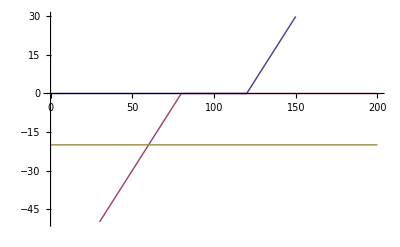

```mathematica
Plot[{
Payoff[MkOption[Position->long, Type->call, Strike->120], S], Payoff[MkOption[Position->short, Type->put, Strike->80], S],
Payoff[MkBond[Position->short,Price->20], S]
}, {S, 0, 200}]
```

```mathematica
Manipulate[Plot[
PortfolioPayoff[{
MkOption[Position->p1, Type->t1, Strike->e1],
MkOption[Position->p2, Type->t2, Strike->e2]}, 
S], {S, 0, 200}, AxesOrigin->{0, 0}], 
"Option1",
Row[{
Control[{{p1, "long", ""}, {"long", "short"}}], 
Control[{{t1, "call", ""}, {"call", "put"}}], 
Control[{{e1, 80, ""}, 0, 200}],
Spacer[10],
Dynamic[e1]
}],
"Option 2",
Row[{
Control[{{p2, "short", ""},{"long", "short"}}],
Control[{{t2, "call", ""}, {"call", "put"}}],
Control[{{e2, 100, ""}, 0, 200}],
Spacer[10],
Dynamic[e2]
}]]
```

```mathematica
Manipulate[Plot[
PortfolioPayoff[{
MkOption[Position->p1, Type->t1, Strike->e1],
MkOption[Position->p2, Type->t2, Strike->e2],
MkOption[Position->p3, Type->t3, Strike->e3]}, 
S], {S, 0, 200}, AxesOrigin->{0, 0}], 
"Option1",
Row[{
Control[{{p1, "long", ""}, {"long", "short"}}], 
Control[{{t1, "call", ""}, {"call", "put"}}], 
Control[{{e1, 80, ""}, 0, 200}],
Spacer[10],
Dynamic[e1]
}],
"Option 2",
Row[{
Control[{{p2, "short", ""},{"long", "short"}}],
Control[{{t2, "call", ""}, {"call", "put"}}],
Control[{{e2, 100, ""}, 0, 200}],
Spacer[10],
Dynamic[e2]
}],
"Option 3",
Row[{
Control[{{p3, "short", ""},{"long", "short"}}],
Control[{{t3, "call", ""}, {"call", "put"}}],
Control[{{e3, 120, ""}, 0, 200}],
Spacer[10],
Dynamic[e3]
}]
]
```